```mathematica
Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"];

InstallFeynCalc[]
```

Welcome to the automatic FeynCalc installer brought to you by the FeynCalc developer team!

• To install the current stable version of FeynCalc (recommended for productive use), please evaluate

InstallFeynCalc[]

• To install the development version of FeynCalc (only for experts or beta testers), please evaluate

InstallFeynCalc[InstallFeynCalcDevelopmentVersion->True]

Global`$LoadAddOns::shdw: Symbol $LoadAddOns appears in multiple contexts {Global`,FeynCalc`}; definitions in context Global` may shadow or be shadowed by other definitions.

$Aborted

```mathematica
description="Gl Gl -> Gl Gl, QCD, matrix element squared, tree";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts"};
Get["FeynCalc`"]
$FAVerbose=0;
FCCheckVersion[9,3,0];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
```

```mathematica
a //MatrixForm
```

TopologyList(Process→{V(5,{Glu1}),V(5,{Glu2})}→{V(5,{Glu3}),V(5,{Glu4})},Model→{SMQCD},GenericModel→{Lorentz},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{})(Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(4)(5),Field(1)),Propagator(Incoming)(Vertex(1)(2),Vertex(4)(5),Field(2)),Propagator(Outgoing)(Vertex(1)(3),Vertex(4)(5),Field(3)),Propagator(Outgoing)(Vertex(1)(4),Vertex(4)(5),Field(4)))→Insertions(Generic)(FeynmanGraph(1,Generic==1)(Field(1)→V(5,{Glu1}),Field(2)→V(5,{Glu2}),Field(3)→V(5,{Glu3}),Field(4)→V(5,{Glu4}))→Insertions(Classes)(FeynmanGraph(1,Classes==1)(Field(1)→V(5,{Glu1}),Field(2)→V(5,{Glu2}),Field(3)→V(5,{Glu3}),Field(4)→V(5,{Glu4})))),Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(3)(5),Field(1)),Propagator(Incoming)(Vertex(1)(2),Vertex(3)(5),Field(2)),Propagator(Outgoing)(Vertex(1)(3),Vertex(3)(6),Field(3)),Propagator(Outgoing)(Vertex(1)(4),Vertex(3)(6),Field(4)),Propagator(Internal)(Vertex(3)(5),Vertex(3)(6),Field(5)))→Insertions(Generic)(FeynmanGraph(1,Generic==1)(Field(1)→V(5,{Glu1}),Field(2)→V(5,{Glu2}),Field(3)→V(5,{Glu3}),Field(4)→V(5,{Glu4}),Field(5)→V)→Insertions(Classes)(FeynmanGraph(1,Classes==1)(Field(1)→V(5,{Glu1}),Field(2)→V(5,{Glu2}),Field(3)→V(5,{Glu3}),Field(4)→V(5,{Glu4}),Field(5)→V(5,{Glu5})))),Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(3)(5),Field(1)),Propagator(Incoming)(Vertex(1)(2),Vertex(3)(6),Field(2)),Propagator(Outgoing)(Vertex(1)(3),Vertex(3)(5),Field(3)),Propagator(Outgoing)(Vertex(1)(4),Vertex(3)(6),Field(4)),Propagator(Internal)(Vertex(3)(5),Vertex(3)(6),Field(5)))→Insertions(Generic)(FeynmanGraph(1,Generic==1)(Field(1)→V(5,{Glu1}),Field(2)→V(5,{Glu2}),Field(3)→V(5,{Glu3}),Field(4)→V(5,{Glu4}),Field(5)→V)→Insertions(Classes)(FeynmanGraph(1,Classes==1)(Field(1)→V(5,{Glu1}),Field(2)→V(5,{Glu2}),Field(3)→V(5,{Glu3}),Field(4)→V(5,{Glu4}),Field(5)→V(5,{Glu5})))),Topology(1)(Propagator(Incoming)(Vertex(1)(1),Vertex(3)(5),Field(1)),Propagator(Incoming)(Vertex(1)(2),Vertex(3)(6),Field(2)),Propagator(Outgoing)(Vertex(1)(3),Vertex(3)(6),Field(3)),Propagator(Outgoing)(Vertex(1)(4),Vertex(3)(5),Field(4)),Propagator(Internal)(Vertex(3)(5),Vertex(3)(6),Field(5)))→Insertions(Generic)(FeynmanGraph(1,Generic==1)(Field(1)→V(5,{Glu1}),Field(2)→V(5,{Glu2}),Field(3)→V(5,{Glu3}),Field(4)→V(5,{Glu4}),Field(5)→V)→Insertions(Classes)(FeynmanGraph(1,Classes==1)(Field(1)→V(5,{Glu1}),Field(2)→V(5,{Glu2}),Field(3)→V(5,{Glu3}),Field(4)→V(5,{Glu4}),Field(5)→V(5,{Glu5})))))

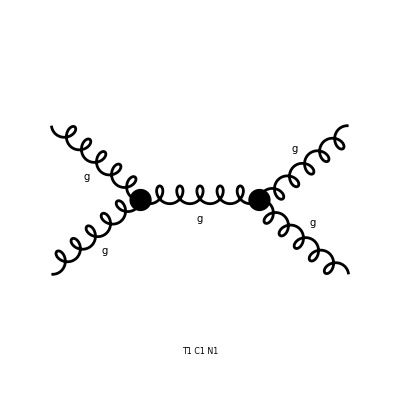

FeynArtsGraphics({g,g}→{g,g})(([T1 C1 N1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
CreateTopologies[0,2->2];
a = InsertFields[%,{V[5],V[5]}->{V[5],V[5]},InsertionLevel->{Classes},Model->"SMQCD"];
Paint[{a[[1]],a[[2]],a[[3]]}];
t2 = DiagramExtract[a,2];
Paint[%]
```

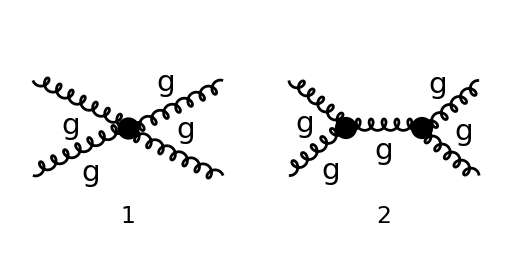

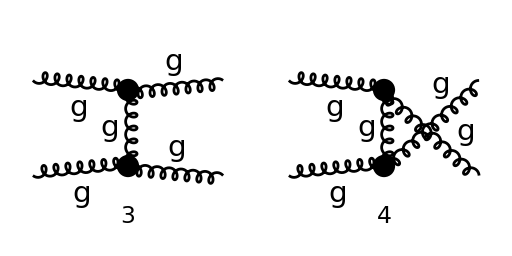

```mathematica
diags=InsertFields[CreateTopologies[0,2->2],{V[5],V[5]}->{V[5],V[5]},InsertionLevel->{Classes},Model->"SMQCD"];
Paint[diags,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp[0] = FCFAConvert[CreateFeynAmp[t2],IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},ChangeDimension->4,TransversePolarizationVectors->{k1,k2,p1,p2},List->True,SMP->True,DropSumOver->True,Contract->True]
```

{-1/(OverBar[p1]+OverBar[p2])^2 g_s^2 f^Glu1Glu2Glu5 f^Glu3Glu4Glu5 (-2 (OverBar[p1]·(ε̄)^*(p2)) ((ε̄(k_1)·(ε̄)^*(p1)) (OverBar[p1]·ε̄(k_2)+OverBar[p2]·ε̄(k_2)+OverBar[k_1]·ε̄(k_2))+(ε̄(k_2)·(ε̄)^*(p1)) (-OverBar[p1]·ε̄(k_1)-OverBar[p2]·ε̄(k_1)-(OverBar[k_2]·ε̄(k_1)))+(ε̄(k_1)·ε̄(k_2)) (OverBar[k_2]·(ε̄)^*(p1)-OverBar[k_1]·(ε̄)^*(p1)))+2 (OverBar[p2]·(ε̄)^*(p1)) ((ε̄(k_1)·(ε̄)^*(p2)) (OverBar[p1]·ε̄(k_2)+OverBar[p2]·ε̄(k_2)+OverBar[k_1]·ε̄(k_2))+(ε̄(k_2)·(ε̄)^*(p2)) (-OverBar[p1]·ε̄(k_1)-OverBar[p2]·ε̄(k_1)-(OverBar[k_2]·ε̄(k_1)))+(ε̄(k_1)·ε̄(k_2)) (OverBar[k_2]·(ε̄)^*(p2)-OverBar[k_1]·(ε̄)^*(p2)))+((ε̄)^*(p1)·(ε̄)^*(p2)) ((OverBar[p1]·ε̄(k_2)-OverBar[p2]·ε̄(k_2)) (-OverBar[p1]·ε̄(k_1)-OverBar[p2]·ε̄(k_1)-(OverBar[k_2]·ε̄(k_1)))+(OverBar[p1]·ε̄(k_1)-OverBar[p2]·ε̄(k_1)) (OverBar[p1]·ε̄(k_2)+OverBar[p2]·ε̄(k_2)+OverBar[k_1]·ε̄(k_2))+(u-t) (ε̄(k_1)·ε̄(k_2))))}

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[t2],IncomingMomenta->{k1,k2},OutgoingMomenta->{k3,k4},UndoChiralSplittings->True,ChangeDimension->4,TransversePolarizationVectors->{k1,k2,k3,k4},List->True,SMP->True,Contract->True,DropSumOver->True]
```

{-1/(OverBar[k_3]+OverBar[k_4])^2 g_s^2 f^Glu1Glu2Glu5 f^Glu3Glu4Glu5 (-2 (OverBar[k_3]·(ε̄)^*(k_4)) ((ε̄(k_1)·ε̄(k_2)) (OverBar[k_2]·(ε̄)^*(k_3)-OverBar[k_1]·(ε̄)^*(k_3))+(ε̄(k_1)·(ε̄)^*(k_3)) (OverBar[k_1]·ε̄(k_2)+OverBar[k_3]·ε̄(k_2)+OverBar[k_4]·ε̄(k_2))+(ε̄(k_2)·(ε̄)^*(k_3)) (-(OverBar[k_2]·ε̄(k_1))-OverBar[k_3]·ε̄(k_1)-OverBar[k_4]·ε̄(k_1)))+2 (OverBar[k_4]·(ε̄)^*(k_3)) ((ε̄(k_1)·(ε̄)^*(k_4)) (OverBar[k_1]·ε̄(k_2)+OverBar[k_3]·ε̄(k_2)+OverBar[k_4]·ε̄(k_2))+(ε̄(k_2)·(ε̄)^*(k_4)) (-(OverBar[k_2]·ε̄(k_1))-OverBar[k_3]·ε̄(k_1)-OverBar[k_4]·ε̄(k_1))+(ε̄(k_1)·ε̄(k_2)) (OverBar[k_2]·(ε̄)^*(k_4)-OverBar[k_1]·(ε̄)^*(k_4)))+((ε̄)^*(k_3)·(ε̄)^*(k_4)) ((OverBar[k_3]·ε̄(k_2)-OverBar[k_4]·ε̄(k_2)) (-(OverBar[k_2]·ε̄(k_1))-OverBar[k_3]·ε̄(k_1)-OverBar[k_4]·ε̄(k_1))+(OverBar[k_3]·ε̄(k_1)-OverBar[k_4]·ε̄(k_1)) (OverBar[k_1]·ε̄(k_2)+OverBar[k_3]·ε̄(k_2)+OverBar[k_4]·ε̄(k_2))+(ε̄(k_1)·ε̄(k_2)) (-(OverBar[k_1]·OverBar[k_3])+OverBar[k_1]·OverBar[k_4]+OverBar[k_2]·OverBar[k_3]-OverBar[k_2]·OverBar[k_4])))}

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,k1,k2,p1,p2,0,0,0,0];
```

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,k1,k2,-k3,-k4,0,0,0,0];
```

```mathematica
amp[0]
```

{-1/(OverBar[p1]+OverBar[p2])^2 g_s^2 f^Glu1Glu2Glu5 f^Glu3Glu4Glu5 (-2 (OverBar[p1]·(ε̄)^*(p2)) ((ε̄(k_1)·(ε̄)^*(p1)) (OverBar[p1]·ε̄(k_2)+OverBar[p2]·ε̄(k_2)+OverBar[k_1]·ε̄(k_2))+(ε̄(k_2)·(ε̄)^*(p1)) (-OverBar[p1]·ε̄(k_1)-OverBar[p2]·ε̄(k_1)-(OverBar[k_2]·ε̄(k_1)))+(ε̄(k_1)·ε̄(k_2)) (OverBar[k_2]·(ε̄)^*(p1)-OverBar[k_1]·(ε̄)^*(p1)))+2 (OverBar[p2]·(ε̄)^*(p1)) ((ε̄(k_1)·(ε̄)^*(p2)) (OverBar[p1]·ε̄(k_2)+OverBar[p2]·ε̄(k_2)+OverBar[k_1]·ε̄(k_2))+(ε̄(k_2)·(ε̄)^*(p2)) (-OverBar[p1]·ε̄(k_1)-OverBar[p2]·ε̄(k_1)-(OverBar[k_2]·ε̄(k_1)))+(ε̄(k_1)·ε̄(k_2)) (OverBar[k_2]·(ε̄)^*(p2)-OverBar[k_1]·(ε̄)^*(p2)))+((ε̄)^*(p1)·(ε̄)^*(p2)) ((OverBar[p1]·ε̄(k_2)-OverBar[p2]·ε̄(k_2)) (-OverBar[p1]·ε̄(k_1)-OverBar[p2]·ε̄(k_1)-(OverBar[k_2]·ε̄(k_1)))+(OverBar[p1]·ε̄(k_1)-OverBar[p2]·ε̄(k_1)) (OverBar[p1]·ε̄(k_2)+OverBar[p2]·ε̄(k_2)+OverBar[k_1]·ε̄(k_2))+(u-t) (ε̄(k_1)·ε̄(k_2))))}